54.8812

0.566465

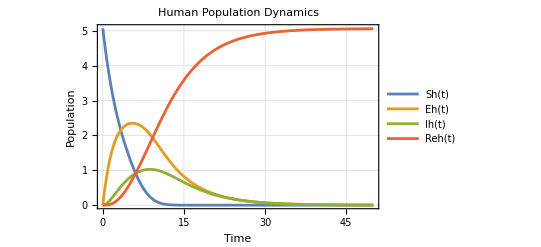

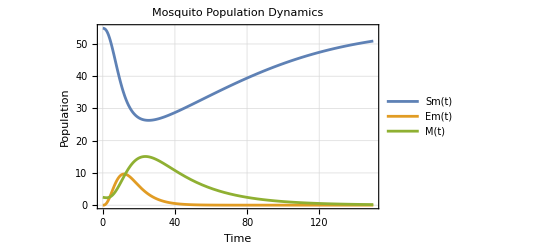

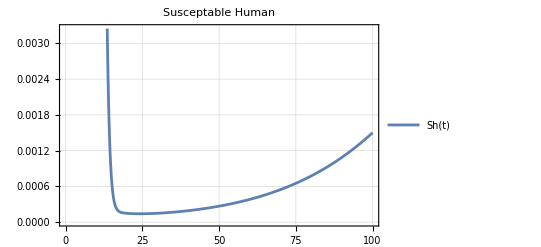

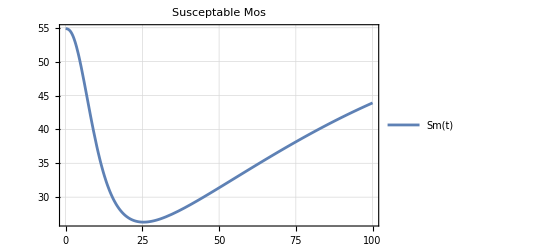

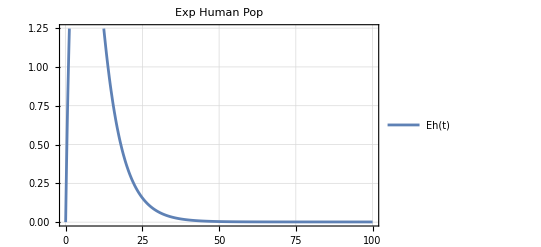

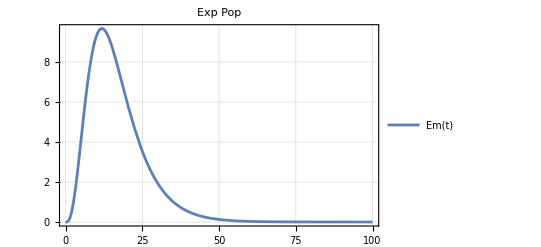

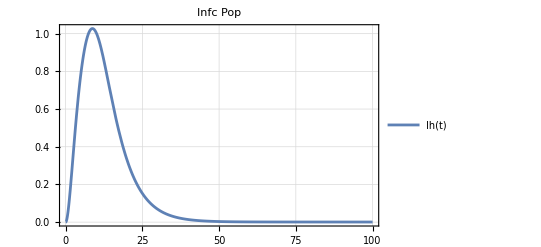

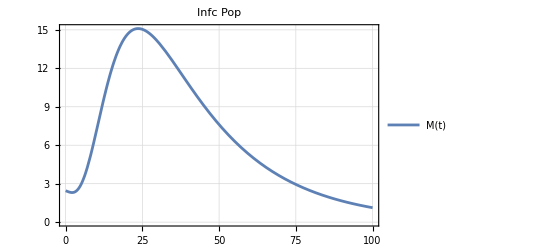

```mathematica
(*Dengue with human behaviour and Carrying capacity*)
(*Para f Hum Pop*)
Lh=0.000046;   (*growth rt*)
A=0.30;
W=0.30;
b1=0.75;
bh=b1*(ⅇ^-(A));(*infec rt by mos bites*)

alph=0.1667;   (*rt from e to i*)
gh=0.328833;    (*recovery rt*)
muh=0.000046;  (*natural d*)
phih=0.0005;


(*Para f Mos Pop*)
Lm=0.025;    (*growth rt*)
b2=0.375; 
bm=b2*(ⅇ^-(A));    (*infec rt by biting infec h*)
alpm=0.1428;   (*rt frm e to i*)
μ2=0.025;
mum=μ2(ⅇ^(W));
phim=0.00530856625;
K=100;
Km=K*ⅇ^-(W+A)(*final Carrying capacity*)


(*IC*)
init={
(*Initial f hum*)
sh[0]==5.071126,
eh[0]==0,
ih[0]==7*10^-5,
R[0]==0,
nh1[0]==sh[0]+eh[0]+ih[0]+R[0],
(*Initial f mos*)
s[0]==Km,
e[0]==0,
m[0]==2.45,
n2[0]==Km+2.45(*tot mos pop*)
};       
 

(*ODE*)
sol=NDSolve[{sh'[t]==Lh*nh1[t]-(bh*m[t]*sh[t]/nh1[t])-(muh*sh[t]),
eh'[t]==(bh*m[t]*sh[t]/nh1[t])-(muh*eh[t])-(alph*eh[t]),ih'[t]==(alph*eh[t])-(gh*ih[t])-(muh*ih[t])-(phih*ih[t]),
R'[t]==(gh*ih[t])-(muh*R[t]),
nh1'[t]==sh'[t]+eh'[t]+ih'[t]+R'[t],
(*mos*)
s'[t]==(Lm*n2[t]*(1-(n2[t]/Km)))-(bm*ih[t]*s[t]/nh1[t]),e'[t]==(bm*ih[t]*s[t]/nh1[t])-(alpm*e[t])-(mum*e[t]),
m'[t]==(alpm*e[t])-(mum*m[t])-(phim*m[t]),
n2'[t]==s'[t]+e'[t]+m'[t] ,
init},
{sh,eh,ih,R,nh1,s,e,m,n2},{t,0,1000}(*,Method->"StiffnessSwitching"*)];
(*Extracting Diff sol*)
(*For human*)
Sh[t_]:=sh[t]/.sol[[1]];
Eh[t_]:=eh[t]/. sol[[1]];
Ih[t_]:=ih[t]/. sol[[1]];
Reh[t_]:=R[t]/. sol[[1]];

(*For mos*)
Sm[t_]:=s[t]/. sol[[1]];
Em[t_]:=e[t]/.sol[[1]];
M[t_]:=m[t]/. sol[[1]];


(*both tot plot*)
Plot[{Sh[t],Eh[t],Ih[t],Reh[t]}, {t,0,50},Frame->True,FrameLabel->{"Time","Population"},PlotTheme->"Detailed",PlotLabel->"Human Population Dynamics" ]
Plot[{Sm[t],Em[t],M[t]}, {t,0,150},Frame->True,FrameLabel->{"Time","Population"},PlotTheme->"Detailed",PlotLabel->"Mosquito Population Dynamics" ]

(*both idi plot*)
Plot[{Sh[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Susceptable Human" ]
Plot[{Sm[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Susceptable Mos" ]

Plot[{Eh[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Exp Human Pop" ]
Plot[{Em[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Exp Pop" ]

Plot[{Ih[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Infc Pop" ]
Plot[{M[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Infc Pop" ]

Plot[{Reh[t]}, {t,0,100},PlotTheme->"Detailed",PlotLabel->"Recovered Pop" ]
```

```mathematica
1.2664469197579094
```

1.26645